OneDrive\Documents\project_code\rl_fluctuations-main\rl_fluctuations-main\ratchet_ppo\roots_table_hyper_r_1_A.csv

OneDrive\Documents\project_code\rl_fluctuations-main\rl_fluctuations-main\ratchet_ppo\roots_table_hyper_r_1_B.csv

OneDrive\Documents\project_code\rl_fluctuations-main\rl_fluctuations-main\ratchet_ppo\roots_table_hyper_r_1.csv

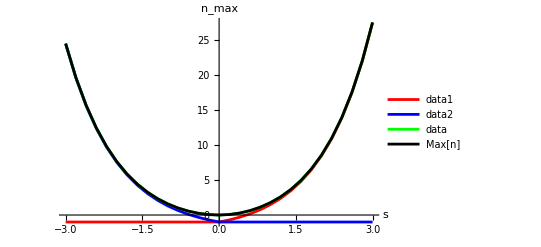

```mathematica
ClearAll["Global`*"]
p1=1;
p2=2;
r=1;
psi1=0.5((p1 /(p1+r+n))+(p2/(p2+r+n)));
psi2= (2  p1  p2)/(((r+n)(p1+p2))+(2  p1  p2));
A=((r (1-psi1))/ ((r+n)(1-(Exp[s]psi1))));
B=((r (1- psi2))/ ((r+n)(1-(Exp[-s]psi2))));
data1=Table[Module[{roots,MaxrealRoot},roots=n /. NSolve[(r+n)(1-(Exp[s]psi1))==0,n];MaxrealRoot=Max@Select[N[roots],Element[#,Reals]&]],{s,-3,3,0.2}];
data2=Table[Module[{roots,MaxrealRoot},roots=n /. NSolve[(r+n)(1-(Exp[-s]psi2))==0,n];MaxrealRoot=Max@Select[N[roots],Element[#,Reals]&]],{s,-3,3,0.2}];

data=Table[Module[{roots,MaxrealRoot},roots=n /. NSolve[(A B)-1 ==0,n];MaxrealRoot=Max@Select[N[roots],Element[#,Reals]&]],{s,-3,3,0.2}];

csvData1=Prepend[data1,{"s","MaxrealRoot"}];
csvData2=Prepend[data2,{"s","MaxrealRoot"}];
csvData=Prepend[data,{"s","MaxrealRoot"}];
Export["OneDrive\\Documents\\project_code\\rl_fluctuations-main\\rl_fluctuations-main\\ratchet_ppo\\roots_table_hyper_r_1_A.csv",csvData1]
Export["OneDrive\\Documents\\project_code\\rl_fluctuations-main\\rl_fluctuations-main\\ratchet_ppo\\roots_table_hyper_r_1_B.csv",csvData2]
Export["OneDrive\\Documents\\project_code\\rl_fluctuations-main\\rl_fluctuations-main\\ratchet_ppo\\roots_table_hyper_r_1.csv",csvData]
sValues=Range[-3,3,0.2];
                 maxRoot=Table[Max[{data1[[i]],data2[[i]],data[[i]]}],{i,Length[data]}];
ListLinePlot[{Transpose[{sValues,data1}],Transpose[{sValues,data2}],Transpose[{sValues,data}]},PlotStyle->{Blue,Green,Black},PlotLegends->{TraditionalForm[Subsuperscript["ν","*","+"]],TraditionalForm[Subsuperscript["ν","*","-"]],TraditionalForm[Subscript ["ν","*"]]},PlotRange->All,AxesLabel->{"s","ν(s)"}]
```

```mathematica
"OneDrive\\Documents\\project_code\\rl_fluctuations-main\\rl_fluctuations-main\\ratchet_ppo\\roots_table_hyper_r_1_A.csv"
```

OneDrive\Documents\project_code\rl_fluctuations-main\rl_fluctuations-main\ratchet_ppo\roots_table_hyper_r_2_blow_up_B.csv

OneDrive\Documents\project_code\rl_fluctuations-main\rl_fluctuations-main\ratchet_ppo\roots_table_hyper_r_2_blow_up.csv